```mathematica
Needs["kColorConnectivity`"]
```

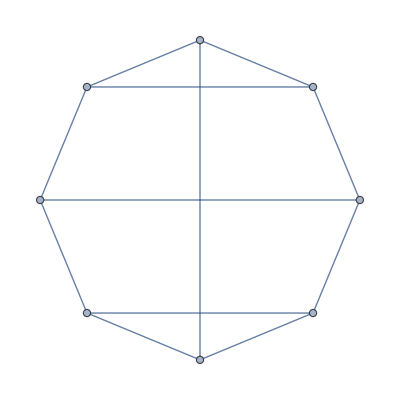
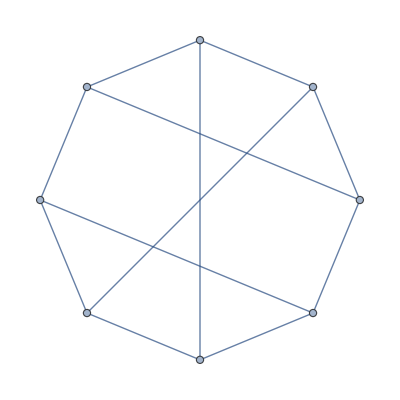

{14.4567,Null}

```mathematica
AbsoluteTiming[CompleteGraphEdgeAdder[8,4,7]]
```

```mathematica
Fit[{0.137529,1.306295,14.456712},n^2,n]
```

1.38238 n^2

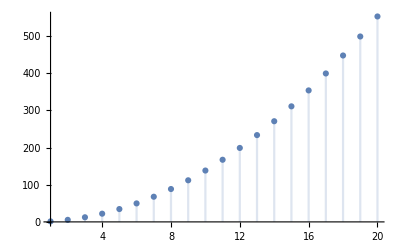

```mathematica
DiscretePlot[1.3823787448979592 n^2,{n,1,20}]
```

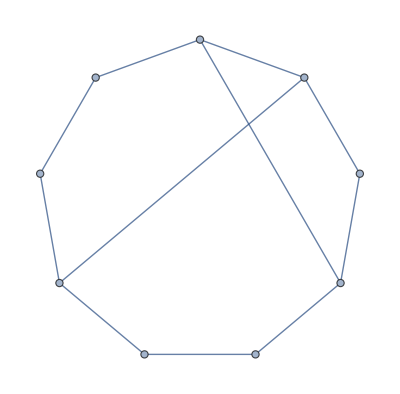
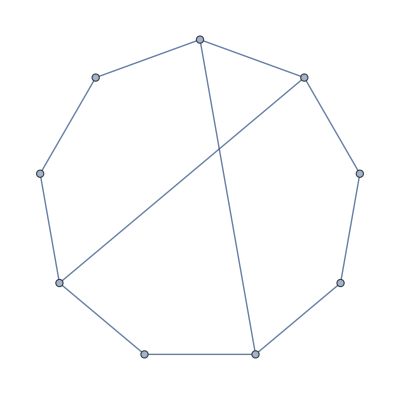
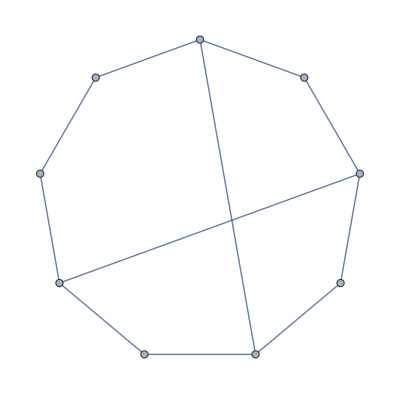

{0.204078,Null}

```mathematica
AbsoluteTiming[CompleteGraphEdgeAdder[9,2,6]]
```

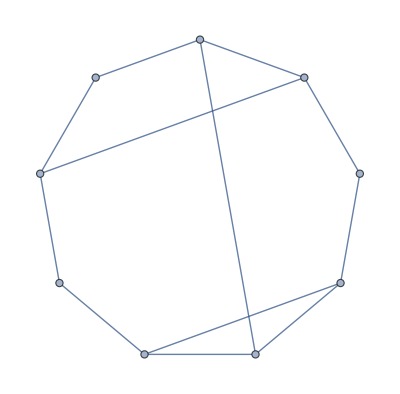
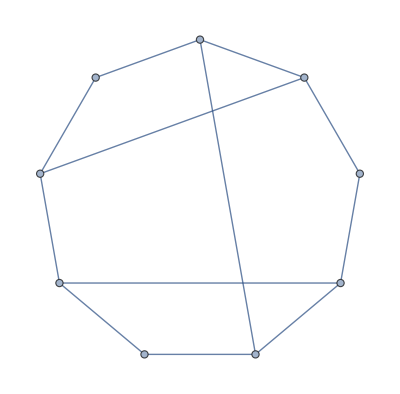
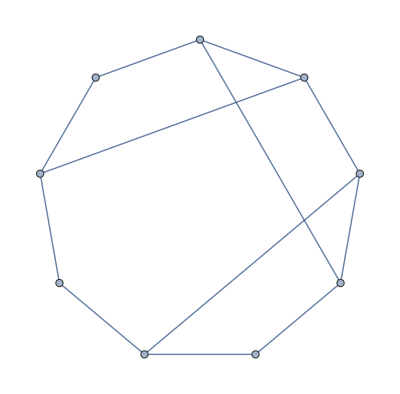

{6.13754,Null}

```mathematica
AbsoluteTiming[CompleteGraphEdgeAdder[9,3,7]]
```

```mathematica
AbsoluteTiming[CompleteGraphEdgeAdder[9,5,8]]
```

$Aborted

```mathematica
{0.204078,6.137535}
```

```mathematica
AbsoluteTiming[chordsFunction[6,2,4]]
```

{0.056381,{{1<->3,2<->5},{1<->4,2<->5},{1<->4,2<->6},{1<->4,3<->5},{1<->4,3<->6},{1<->5,3<->6},{2<->4,3<->6},{2<->5,3<->6},{2<->5,4<->6}}}

```mathematica
AbsoluteTiming[chordsFunction[6,3,5]]
```

{0.074685,{{1<->3,2<->5,4<->6},{1<->4,2<->6,3<->5},{1<->5,2<->4,3<->6}}}

```mathematica
AbsoluteTiming[chordsFunction[7,2,5]]
```

{0.131036,{{1<->4,2<->6},{1<->4,3<->6},{1<->5,3<->6},{1<->5,3<->7},{2<->5,3<->7},{2<->5,4<->7},{2<->6,4<->7}}}

```mathematica
AbsoluteTiming[chordsFunction[7,4,6]]
```

{7.48641,{{1<->3,1<->4,2<->6,5<->7},{1<->3,1<->5,2<->7,4<->6},{1<->3,1<->6,2<->5,4<->7},{1<->3,2<->4,2<->6,5<->7},{1<->3,2<->4,3<->6,5<->7},{1<->3,2<->5,2<->6,4<->7},{1<->3,2<->5,2<->7,4<->6},{1<->3,2<->5,3<->7,4<->6},{1<->3,2<->5,4<->6,4<->7},{1<->3,2<->5,4<->6,5<->7},{1<->3,2<->6,3<->5,4<->7},{1<->3,2<->6,4<->6,5<->7},{1<->3,2<->6,4<->7,5<->7},{1<->4,1<->5,2<->7,3<->6},{1<->4,1<->6,2<->7,3<->5},{1<->4,2<->4,3<->6,5<->7},{1<->4,2<->6,2<->7,3<->5},{1<->4,2<->6,3<->5,4<->7},{1<->4,2<->6,3<->5,5<->7},{1<->4,2<->6,3<->6,5<->7},{1<->4,2<->7,3<->5,3<->6},{1<->4,2<->7,3<->5,4<->6},{1<->4,2<->7,3<->6,5<->7},{1<->5,1<->6,2<->4,3<->7},{1<->5,2<->4,2<->7,3<->6},{1<->5,2<->4,3<->6,3<->7},{1<->5,2<->4,3<->6,5<->7},{1<->5,2<->4,3<->7,4<->6},{1<->5,2<->5,3<->7,4<->6},{1<->5,2<->7,3<->5,4<->6},{1<->5,2<->7,3<->6,4<->6},{1<->5,2<->7,3<->7,4<->6},{1<->6,2<->4,2<->5,3<->7},{1<->6,2<->4,3<->5,3<->7},{1<->6,2<->4,3<->5,4<->7},{1<->6,2<->4,3<->6,5<->7},{1<->6,2<->4,3<->7,5<->7},{1<->6,2<->5,3<->5,4<->7},{1<->6,2<->5,3<->7,4<->6},{1<->6,2<->5,3<->7,4<->7},{1<->6,2<->6,3<->5,4<->7},{1<->6,2<->7,3<->5,4<->7}}}

```mathematica
AbsoluteTiming[chordsFunction[8,2,5]]
```

{1.14948,{{1<->3,2<->6},{1<->4,2<->6},{1<->4,2<->7},{1<->4,3<->6},{1<->4,3<->7},{1<->5,2<->6},{1<->5,2<->7},{1<->5,2<->8},{1<->5,3<->6},{1<->5,3<->7},{1<->5,3<->8},{1<->5,4<->6},{1<->5,4<->7},{1<->5,4<->8},{1<->6,3<->7},{1<->6,3<->8},{1<->6,4<->7},{1<->6,4<->8},{1<->7,4<->8},{2<->4,3<->7},{2<->5,3<->7},{2<->5,3<->8},{2<->5,4<->7},{2<->5,4<->8},{2<->6,3<->7},{2<->6,3<->8},{2<->6,4<->7},{2<->6,4<->8},{2<->6,5<->7},{2<->6,5<->8},{2<->7,4<->8},{2<->7,5<->8},{3<->5,4<->8},{3<->6,4<->8},{3<->6,5<->8},{3<->7,4<->8},{3<->7,5<->8},{3<->7,6<->8}}}

```mathematica
AbsoluteTiming[chordsFunction[8,3,6]]
```

{16.6429,{{1<->3,2<->5,2<->7},{1<->3,2<->5,4<->7},{1<->3,2<->6,4<->7},{1<->3,2<->6,4<->8},{1<->3,2<->6,5<->7},{1<->3,2<->6,5<->8},{1<->3,2<->7,5<->8},{1<->4,1<->5,2<->7},{1<->4,1<->6,2<->8},{1<->4,2<->6,2<->7},{1<->4,2<->6,3<->7},{1<->4,2<->6,5<->7},{1<->4,2<->7,3<->5},{1<->4,2<->7,3<->6},{1<->4,2<->7,5<->8},{1<->4,2<->7,6<->8},{1<->4,2<->8,3<->6},{1<->4,3<->5,4<->7},{1<->4,3<->6,3<->7},{1<->4,3<->6,4<->8},{1<->4,3<->6,5<->7},{1<->4,3<->6,5<->8},{1<->4,3<->7,6<->8},{1<->5,1<->6,3<->8},{1<->5,2<->4,3<->7},{1<->5,2<->5,4<->7},{1<->5,2<->6,3<->7},{1<->5,2<->6,3<->8},{1<->5,2<->6,4<->7},{1<->5,2<->6,4<->8},{1<->5,2<->7,4<->6},{1<->5,2<->7,4<->8},{1<->5,2<->8,3<->6},{1<->5,2<->8,3<->7},{1<->5,2<->8,4<->6},{1<->5,2<->8,4<->7},{1<->5,3<->6,4<->8},{1<->5,3<->6,5<->8},{1<->5,3<->7,4<->6},{1<->5,3<->7,4<->8},{1<->5,3<->7,6<->8},{1<->5,3<->8,4<->6},{1<->6,2<->4,3<->7},{1<->6,2<->4,3<->8},{1<->6,2<->5,3<->8},{1<->6,2<->5,4<->7},{1<->6,2<->6,4<->7},{1<->6,2<->8,4<->7},{1<->6,3<->5,4<->7},{1<->6,3<->5,4<->8},{1<->6,3<->6,5<->7},{1<->6,3<->7,4<->7},{1<->6,3<->7,4<->8},{1<->6,3<->8,4<->7},{1<->6,3<->8,4<->8},{1<->6,3<->8,5<->7},{1<->7,2<->5,3<->8},{1<->7,2<->5,4<->8},{1<->7,2<->6,4<->8},{1<->7,3<->5,4<->8},{1<->7,3<->6,4<->8},{1<->7,3<->6,5<->8},{1<->7,3<->8,5<->8},{2<->4,3<->6,3<->8},{2<->4,3<->6,5<->8},{2<->4,3<->7,5<->8},{2<->4,3<->7,6<->8},{2<->5,2<->6,3<->8},{2<->5,3<->7,3<->8},{2<->5,3<->7,4<->8},{2<->5,3<->7,6<->8},{2<->5,3<->8,4<->6},{2<->5,3<->8,4<->7},{2<->5,4<->6,5<->8},{2<->5,4<->7,4<->8},{2<->5,4<->7,6<->8},{2<->6,3<->5,4<->8},{2<->6,3<->6,5<->8},{2<->6,3<->7,4<->8},{2<->6,3<->7,5<->8},{2<->6,3<->8,5<->7},{2<->6,4<->8,5<->7},{2<->7,3<->5,4<->8},{2<->7,3<->6,5<->8},{2<->7,3<->7,5<->8},{2<->7,4<->6,5<->8},{2<->7,4<->7,6<->8},{2<->7,4<->8,5<->8}}}

```mathematica
AbsoluteTiming[chordsFunction[8,4,7]]
```

{20.0511,{{1<->3,2<->5,4<->7,6<->8},{1<->3,2<->6,4<->8,5<->7},{1<->3,2<->7,4<->6,5<->8},{1<->4,2<->6,3<->7,5<->8},{1<->4,2<->7,3<->5,6<->8},{1<->4,2<->8,3<->6,5<->7},{1<->5,2<->4,3<->7,6<->8},{1<->5,2<->6,3<->7,4<->8},{1<->5,2<->6,3<->8,4<->7},{1<->5,2<->7,3<->6,4<->8},{1<->5,2<->8,3<->7,4<->6},{1<->6,2<->4,3<->8,5<->7},{1<->6,2<->5,3<->7,4<->8},{1<->6,2<->8,3<->5,4<->7},{1<->7,2<->4,3<->6,5<->8},{1<->7,2<->5,3<->8,4<->6},{1<->7,2<->6,3<->5,4<->8}}}

```mathematica
AbsoluteTiming[chordsFunction[9,2,6]]
```

{2.23445,{{1<->4,2<->7},{1<->4,3<->7},{1<->5,2<->7},{1<->5,2<->8},{1<->5,3<->7},{1<->5,3<->8},{1<->5,4<->7},{1<->5,4<->8},{1<->6,3<->7},{1<->6,3<->8},{1<->6,3<->9},{1<->6,4<->7},{1<->6,4<->8},{1<->6,4<->9},{1<->7,4<->8},{1<->7,4<->9},{2<->5,3<->8},{2<->5,4<->8},{2<->6,3<->8},{2<->6,3<->9},{2<->6,4<->8},{2<->6,4<->9},{2<->6,5<->8},{2<->6,5<->9},{2<->7,4<->8},{2<->7,4<->9},{2<->7,5<->8},{2<->7,5<->9},{2<->8,5<->9},{3<->6,4<->9},{3<->6,5<->9},{3<->7,4<->9},{3<->7,5<->9},{3<->7,6<->9},{3<->8,5<->9},{3<->8,6<->9}}}

```mathematica
AbsoluteTiming[chordsFunction[9,5,8]]
```

$Aborted

```mathematica
AbsoluteTiming[chordsFunction[10,2,6]]
```